Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

Note: I should make a statement explaining that my viewpoint differs from the text on the matter of iteration techniques like the ones in this section. I do not desire to run through all the steps of the Newton or Secant methods in detail. If Mathematica can do what is needed inside a black box, that is fine with me. All I want to know is which black box it is, and the conditions under which it is expected to work correctly.

```mathematica
Clear["Global`*"]
```

1 - 13 Fixed-point iteration
Solve by fixed-point iteration and answer related questions where indicated.

3.  f = x - 0.5 Cos[x] = 0, x_0 = 1. Sketch.

```mathematica
Clear["Global`*"]
```

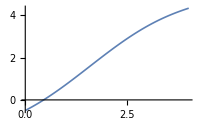

```mathematica
Plot[x-0.5 Cos[x],{x,0,4},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
Simplify[x-0.5 Cos[x]]
```

x-0.5 Cos[x]

According the explanation in the document center for FindRoot, entering one guess value turns on Newton’s method. (Inserting two guess values invokes a variant of the secant method.) When I saw a precision attribute mentioned in the text answer I thought about putting in a precision goal, but Mathematica’s default precision is good enough, probably, for all these problems. As for the guess x_0, in this case it was not chosen with consideration.

```mathematica
FindRoot[x-0.5 Cos[x],{x,1}]
```

{x→0.450184}

Let me try to find g[x]. According to material at https://mat.iitm.ac.in/home/sryedida/public_html/caimna/transcendental/iteration%20methods/fixed-point/iteration.html it is basically just a process of getting x on one side of the equals sign and everything else on the other side. (Wikipedia has a more complicated calculation, dealing with derivatives, such that g[x] might be equal to x - f[x]/f'[x]).

Using the first method gives me g[x] = 0.5 Cos[x], which agrees with the text answer.

5.  Sketch f[x] = x^3 - 5.00 x^2 + 1.01 x + 1.88, showing roots near ±1 and 5. Write x = g[x] = (5.00 x^2-1.01 x + 1.88)/x^2. Find a root by starting from x_0 = 5, 4, 1, -1. Explain the (perhaps unexpected) results.

```mathematica
Clear["Global`*"]
```

First of all, there appears to be a typo in the problem description. The suggested form of g[x] has an incorrect sign for the last constant. Shouldn’t that be "-1.88”?

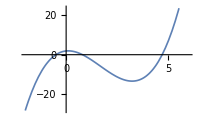

```mathematica
Plot[x^3-5.00 x^2+1.01 x+1.88,{x,-2,6},ImageSize->200,PlotStyle->Thickness[0.006]]
```

It looks like the root is at approximately 0.8 on the x-axis.

```mathematica
FindRoot[x^3-5.00 x^2+1.01 x+1.88,{x,0.7}]
```

{x→0.8}

```mathematica
x^3-5.00 x^2+1.01 x+1.88/.x->0.8
```

-8.88178×10^-16

The quantity shown above is very small, less than 10^-10. The default Chop chop would chop it. But I have not covered all the problem instructions. I need to try out the x_0 values provided. I seem to remember that a 3rd degree polynomial is expected to have three roots. Apparently, the first two test values are shifted to the right far enough to catch the largest root.

```mathematica
FindRoot[x^3-5.00 x^2+1.01 x+1.88,{x,5}]
```

{x→4.7}

```mathematica
FindRoot[x^3-5.00 x^2+1.01 x+1.88,{x,4}]
```

{x→4.7}

The next suggested root is close enough to the middle root to retrieve that one.

```mathematica
FindRoot[x^3-5.00 x^2+1.01 x+1.88,{x,1}]
```

{x→0.8}

And for the last root, FindRoot again finds the closest root to the guess value.

```mathematica
FindRoot[x^3-5.00 x^2+1.01 x+1.88,{x,-1}]
```

{x→-0.5}

```mathematica
x^3-5.00 x^2+1.01 x+1.88/.x->-0.5000000000000011
```

-7.77156×10^-15

Yes. The guess value of x_0 was close enough to the left root to trigger a successful search there.

7.  Find the smallest positive solution of Sin[x] = ⅇ^-x .

```mathematica
Clear["Global`*"]
```

The periodic nature of the sine function takes over in the positive domain. It looks like the smallest positive root falls at about 0.7.

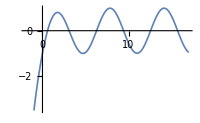

```mathematica
Plot[Sin[x]-ⅇ^-x,{x,-2,17},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
FindRoot[Sin[x]-ⅇ^-x,{x,0.7}]
```

{x→0.588533}

The location of the root on the plot was a little misleading, I think, at least at the plot size I requested.

```mathematica
Sin[x]-ⅇ^-x/.x->0.5885327439818611
```

0.

9.  Find the negative solution of x^4 - x - 0.12 = 0.

```mathematica
Clear["Global`*"]
```

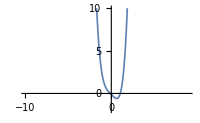

```mathematica
Plot[x^4-x-0.12,{x,-10,9},PlotRange->{{-10,9},{-2,10}},ImageSize->200,PlotStyle->Thickness[0.006]]
```

By choosing a particular plot range this function comes into focus.

```mathematica
FindRoot[x^4-x-0.12,{x,-0.1}]
```

{x→-0.119794}

```mathematica
x^4-x-0.12/.x->-0.11979405979852116
```

-3.90313×10^-18

11.  Drumhead. Bessel functions. A partial sum of the Maclaurin series of J_0[x] (section 5.5) is f[x] = 1 -1/4 x^2 + 1/64 x^4 - 1/2304 x^6. Conclude from a sketch that f[x] = 0 near x = 2. Write f[x] = 0 as x = g[x] (by dividing f[x] by 1/4 x and taking the resulting x-term to the other side). Find the zero. (See section 12.10 for the importance of these zeros.)

```mathematica
Clear["Global`*"]
```

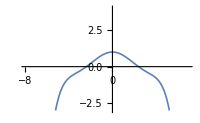

```mathematica
Plot[1-1/4 x^2+1/64 x^4-1/2304 x^6,{x,-10,9},PlotRange->{{-8,7},{-3,4}},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
f[x_]=1-1/4 x^2+1/64 x^4-1/2304 x^6
```

1-x^2/4+x^4/64-x^6/2304

I will build the g[x] function just to humor the text.

```mathematica
g[x_]=Simplify[f[x]/(1/4x)]
```

4/x-x+x^3/16-x^5/576

And check the root of it.

```mathematica
FindRoot[4/x-x+x^3/16-x^5/576,{x,2}]
```

{x→2.39165}

```mathematica
4/x-x+x^3/16-x^5/576/.x->2.391646690891294
```

1.11022×10^-16

But I think that Mathematica is completely capable of skipping the g[x] function in this case.

```mathematica
FindRoot[1-1/4 x^2+1/64 x^4-1/2304 x^6,{x,2}]
```

{x→2.39165}

The text lists a Newton construct, 2.405 4S-exact, as it calls it, but since this is off the green root point by a considerable amount, I don’t understand its value.

13.  Existence of fixed point. Prove that if g is continuous in a closed interval I and its range lies in I, then the equation x = g[x] has at least one solution in I. Illustrate that it may have more than one solution in I.

14 - 23 Newton’s method.

Note: Since as I mentioned FindRoot incorporates Newton’s method, I take the position that I am using it now.

15. f = 2 x - Cos[x], x_0=1. Compare with problem 3.

```mathematica
Clear["Global`*"]
```

The plot shows the current problem (teal) as well as the function of problem 3 (gold).

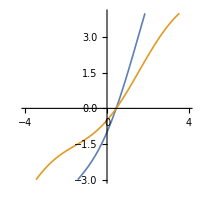

```mathematica
Plot[{2 x-Cos[x],x-0.5Cos[x]},{x,-4,4},PlotRange->{{-4,4},{-3,4}},ImageSize->200,AspectRatio->Automatic,PlotStyle->Thickness[0.006]]
```

Though the root point is not that close to the 1 suggested in the problem, I will use it.

```mathematica
FindRoot[2 x-Cos[x],{x,1}]
```

{x→0.450184}

```mathematica
2 x-Cos[x]/.x->0.4501836112948736
```

1.11022×10^-16

The problem asks that I contemplate the common root betwen problem 3 and problem 15.

17.  Dependence on x_0. Solve problem 5 by Newton’s method with x_0 = 5, 4, 1, -3. Explain the result.

```mathematica
Clear["Global`*"]
```

Just to review the plot,

```mathematica
Plot[x^3-5.00 x^2+1.01 x+1.88,{x,-2,6},ImageSize->200,PlotStyle->Thickness[0.006]]
```

-Graphics-

Since FindRoot with a single guess point uses Newton’s method, the problem has already been worked in problem 5 for all values except for the final x_0 mentioned, -3.

```mathematica
FindRoot[x^3-5.00 x^2+1.01 x+1.88,{x,-3}]
```

{x→-0.5}

The suggested guess point brings me back to the negative-valued root

```mathematica
x^3-5.00 x^2+1.01 x+1.88/.x->-0.5000000000000012
```

-8.43769×10^-15

I notice that Mathematica has changed the 16th place digit from that used before in problem 5, though naturally without any appreciable change in the result.

19.  Associated Legendre functions. Find the smallest positive zero of P_4^2 = (1 - x^2)P_4'' = 15/2(-7 x^4 + 8 x^2 - 1) (section 5.3) (a) by Newton’s method, (b) exactly, by solving a quadratic equation.

```mathematica
Clear["Global`*"]
```

I reviewed section 5.3 briefly, and am now assuming that the P designates a polynomial as described in problem 14 within problem set 5.3. That may be interesting in the realm of hypergeometrics and indicial equations, but at the moment I will try to use only the last part, the expanded polynomial expression.

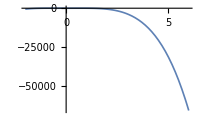

```mathematica
Plot[15/2(-7 x^4+8 x^2-1),{x,-2,6},ImageSize->200,PlotStyle->Thickness[0.006]]
```

After trying a series of one-sies, I think a table is called for

```mathematica
Table[FindRoot[15/2(-7 x^4+8 x^2-1),{x,n}],{n,0,1,0.01}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.}. Try perturbing the initial point(s).

{{x→0.},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→1.},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→0.377964},{x→-0.377964},{x→-0.377964},{x→-0.377964},{x→-1.},{x→0.377964},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.},{x→1.}}

It looks like 0.377964 meets the necessary description for (a).

```mathematica
Reduce[15/2(-7 x^4+8 x^2-1)==0,{x}]
```

x==-1||x==1||x==-1/(√7)||x==1/(√7)

It looks like x==1/(√7) meets the necessary description for (b).

I don’t know that Reduce uses the quadratic equation, but in the document center is the statement, “When expr involves only polynomial equations and inequalities over real or complex domains, then Reduce can always in principle solve directly for all the x_i.”

21.  f = x^3 - 5 x + 3 = 0, x_0 = 2, 0, -2

```mathematica
Clear["Global`*"]
```

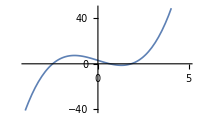

```mathematica
Plot[x^3-5 x+3,{x,-4,5},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
NumberForm[Table[FindRoot[x^3-5 x+3,{x,n}],{n,{-2,0,2}}],{10,6}]
```

{{x→-2.490864},{x→0.656620},{x→1.834243}}

The values in the above cell agree with the text answer. Originally I had the NumberForm parameters set at {6,6}, and the last value did not come out correctly {x→1.834240}. When I raised the precision parameter to 10, I got the text answer value.

23. Vibrating beam. Find the solution of Cos[x] Cosh[x] = 1 near x = 3/2π. (This determines a frequency of a vibrating beam; see problem set 12.3)

```mathematica
Clear["Global`*"]
```

I’m including two plots, the left one relating to the problem request, the right one to a trivial experiment.

```mathematica
p1=Plot[Cos[x] Cosh[x]-1,{x,-4,5},ImageSize->200,PlotStyle->Thickness[0.006]];
```

```mathematica
p2=Plot[Cos[x] Cosh[x]-1,{x,-0.05,0.05},ImageSize->200,PlotStyle->Thickness[0.006],AspectRatio->1,PlotRange->{{-0.04,0.04},{-2*^-8,0.2*^-7}}];
```

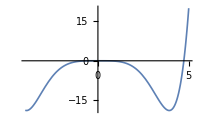
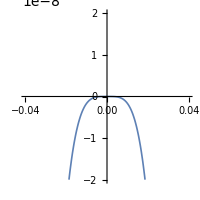

```mathematica
Row[{p1,p2}]
```

Solving the problem request is not difficult.

```mathematica
NumberForm[FindRoot[Cos[x] Cosh[x]-1,{x,4.5,5.}],{10,5}]
```

{x→4.73004}

Apparently I got off easy by being asked for the largest root. As for the thorny one around the origin, I need more Mathematica skills in order to have a chance of getting something useful out of it. If I try

```mathematica
Table[FindRoot[Cos[x] Cosh[x]-1.,{x,n},AccuracyGoal->20,PrecisionGoal->16,MaxIterations->1000],{n,-0.005,0.005,0.0002}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{x→-0.00013127},{x→-0.000159622},{x→-0.0000273773},{x→-0.000144819},{x→-0.000123364},{x→-0.000221738},{x→-0.000155742},{x→-0.000179311},{x→-0.000194984},{x→-0.000172364},{x→-0.000145085},{x→-0.0000820118},{x→-0.000103277},{x→-0.000104055},{x→-0.000220568},{x→-0.0000920962},{x→-0.000173217},{x→-0.0000966512},{x→-0.00018501},{x→-0.000171792},{x→-0.000159081},{x→-0.0000479927},{x→-0.000142951},{x→-0.000098512},{x→-0.000116438},{x→0.},{x→0.000116438},{x→0.000098512},{x→0.000142951},{x→0.0000479927},{x→0.000159081},{x→0.000171792},{x→0.00018501},{x→0.0000966512},{x→0.000173217},{x→0.0000920962},{x→0.000220568},{x→0.000104055},{x→0.000103277},{x→0.0000820118},{x→0.000145085},{x→0.000172364},{x→0.000194984},{x→0.000179311},{x→0.000155742},{x→0.000221738},{x→0.000123364},{x→0.000144819},{x→0.0000273773},{x→0.000159622},{x→0.00013127}}

the results are ambiguous. Whereas

```mathematica
Solve[Cos[x] Cosh[x]-1<10^-10,{x}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-1+Cos[x] Cosh[x]<1/10000000000,{x}]

requires a lot of computing time and still fails.  Maybe an ultra zoomed plot

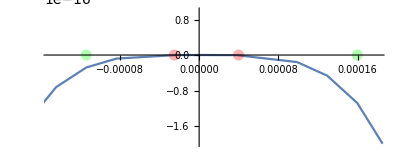

```mathematica
p3=Plot[Cos[x] Cosh[x]-1,{x,-0.05,0.05},ImageSize->400,PlotStyle->Thickness[0.004],AspectRatio->0.4,PlotRange->{{-0.00015,0.00018},{-2*^-16,0.1*^-15}},WorkingPrecision->20,Epilog->{{Green,PointSize[0.02],Opacity[0.3],Point[{-0.000114,0}]},{Red,PointSize[0.02],Opacity[0.3],Point[{-0.000025,0}]},{Red,PointSize[0.02],Opacity[0.3],Point[{0.0000398,0}]},{Green,PointSize[0.02],Opacity[0.3],Point[{0.0001597,0}]}}]
```

would shed some light. Yes, this helps. It tells me that any x in the interval delimited by the two center points shown in the plot has a function value which effectively equals zero. It makes me more disposed to go with a graphic solution to this kind of problem, especially considering that the result comes back almost instantly. (Note: Before I specified a working precision, the green points figured into the zero zone.)

25.  TEAM PROJECT. Bisection method. This simple but slowly convergent method for finding a solution of f[x] = 0 with continuous f is based on the intermediate value theorem, which states that if a continuous function f has opposite signs at some x = a and x = b (>a), that is either f[a] < 0, f[b] > 0, or f[a] > 0, f[b] < 0, then f must be somewhere on [a,b]. The solution is found by repeated bisection of the interval and in each iteration picking that half which also satisfies that sign condition.
(a) Algorithm. Write an algorithm for the method.
(b) Comparison. Solve x = Cos[x] by Newton’s method and by bisection. Compare.
(c) Solve ⅇ^-x = Log[x] and ⅇ^x + x^4 + x = 2 by bisection.

```mathematica
Clear["Global`*"]
```

The (a) part of the problem is addressed below, and was obtained in MMAStackExchange question 69771 in the answer of J.M. is away. It is a bisection function to which I am expected to feed 1. a function name, 2. a search interval, 3. a tolerance allowance, and 4. a number for max iterations.

```mathematica
Bisection[f_,int_,tol_,niter_]:=Block[{m=tol+1,prev,ym,yl=f[Last@int]},NestWhile[(prev=m;
m=Total@#/2;
ym=f[m];
If[ym*yl>0,yl=ym;{First@#,m},{m,Last@#}])&,int,ym≠0&&Abs[m-prev]>tol&,2,niter]]
```

That is all of the bisection code. Now for a short test with the function that was included on-line

```mathematica
func[t_?NumericQ]:=1+NIntegrate[Sin[x^2]-x,{x,0,t}];

Bisection[func,{1,2.`20},10^-14,1000]
```

{1.9252809180739163253,1.9252809180739234307}

Having kicked the tires on the bisection code, I can try it out on my own function, after first making the plot.

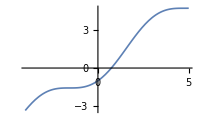

```mathematica
Plot[x-Cos[x],{x,-4,5},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
funct[x_?NumericQ]:=x-Cos[x]
```

```mathematica
Bisection[funct,{0.5,1.},10^-14,1000]
```

{0.739085,0.739085}

I want to try out the bisection code on problem 5, in which were found three separate roots.

```mathematica
funct[x_?NumericQ]:=x^3-5.00 x^2+1.01 x+1.88
```

```mathematica
Bisection[funct,{-1.,5.},10^-14,1000]
```

{4.7,4.7}

Evidently, the bisection function only finds the last root in the interval. That being the case, I don’t understand why it needs to repeat the root.

For part (b) of the problem

```mathematica
NumberForm[FindRoot[x-Cos[x],{x,0.5}],{10,6}]
```

{x→0.739085}

As seen above, the FindRoot answer (Newton’s method), matches the bisection method answer.

For part (c) of the problem, two cases are presented

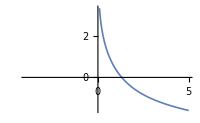

```mathematica
Plot[ⅇ^-x-Log[x],{x,-4,5},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
funct[x_?NumericQ]:=ⅇ^-x-Log[x]
```

```mathematica
NumberForm[Bisection[funct,{1.,1.5},10^-14,1000],{10,5}]
```

{1.30980,1.30980}

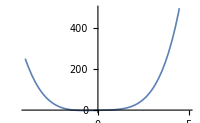

```mathematica
Plot[ⅇ^x+x^4+x-2,{x,-4,5},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
funct[x_?NumericQ]:=ⅇ^x+x^4+x-2
```

```mathematica
NumberForm[Bisection[funct,{-1.,1.},10^-14,1000],{10,6}]
```

{0.429494,0.429494}

26 - 29 Secant method
Solve, using x_0 and x_1 as indicated:

As mentioned above, (a variation of) the secant method is incorporated into FindRoot when two guesses are included.

27.  Problem 21, x_0 = 1.0, x_1 = 2.0

```mathematica
Clear["Global`*"]
```

First repeating the plot

```mathematica
Plot[x^3-5 x+3,{x,-4,5},ImageSize->200,PlotStyle->Thickness[0.006]]
```

-Graphics-

```mathematica
NumberForm[FindRoot[x^3-5 x+3,{x,1.,2.}],{10,5}]
```

{x→1.83424}

```mathematica
FindRoot[x^3-5 x+3,{x,1.,2.}]
```

{x→1.83424}

```mathematica
x^3-5 x+3/.x->1.834243184313922
```

8.88178×10^-16

The above answer matches the text, and shows that the secant (or Brent’s method) works. The pink x substitute was not copied from the result of the NumberForm line, rather from the yellow line below that one. It is both interesting and necessary to understand that NumberForm, while delivering my desired output format, nevertheless drops, internally, all digits beyond what I ask for.

29. Sin[x] = Cot[x], x_0 = 1, x_1 = 0.5

```mathematica
Clear["Global`*"]
```

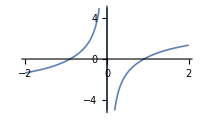

```mathematica
Plot[Sin[x]-Cot[x],{x,-2,2},ImageSize->200,PlotStyle->Thickness[0.006]]
```

```mathematica
NumberForm[FindRoot[Sin[x]-Cot[x],{x,1.,0.5}],{10,6}]
```

{x→0.904557}

```mathematica
FindRoot[Sin[x]-Cot[x],{x,1.,0.5}]
```

{x→0.904557}

```mathematica
Sin[x]-Cot[x]/.x->0.9045568943023813
```

-1.11022×10^-16